Далее в блокноте:
	Ω[β, α] -- частота Раби
	ωR[β, α] -- частота перехода β→α
	ωD -- сдвинутая по Доплеру частота лазера 
	ρ[β, α] -- матричный элемент матрицы плотности
	e -- множество возбужденных состояний
	g -- множество ground состояний
	τ -- время жизни

```mathematica
ClearAll[ρ, α, β, γ, i, j, k, Ω, ωR, ρ0, e, g, τ];
```

```mathematica
g = {1};
e = {2, 3};
nStates = Length@Join[g, e];
```

## Print eq

```mathematica
ClearAll[Eq2Print];
Eq2Print[eq_] := eq /. {
τ -> 1, 
Ω[β_, α_] :>   Subscript["Ω", ToString[β]<>ToString[α]], 
ωR[β_, α_] :> Subscript["ω", ToString[β]<>ToString[α]],
C[β_, α_] :> Subscript["C", ToString[β]<>ToString[α]],
ρ[β_, α_] :> Subscript["ρ", ToString[β]<>ToString[α]],
ωD :> "ω'",
ρRe[β_, α_] :> Subscript["ρ^re", ToString[β]<>ToString[α]],
ρIm[β_, α_] :> Subscript["ρ^im", ToString[β]<>ToString[α]]
};
```

## Релаксационная часть

```mathematica
ClearAll[LPart];
LPart[β_, α_] := -1/(2 τ)ρ0[β, α] /; MemberQ[g, α] && MemberQ[e, β];
LPart[β_, α_] := -1/τ ρ0[β, α]/;α== β && MemberQ[e, β];
LPart[β_, α_] := 1/τ Total@Map[ C[#, α]^2 ρ0[#, #]&, e] /; α == β && MemberQ[g, α];
LPart[β_, α_] := 0;
```

```mathematica
(* пример *)
n = 3;
Table[LPart[i, j], {i, 1, n}, {j, 1, n}] // MatrixForm // FullSimplify // Eq2Print
```

(C_21^2 ρ0[2,2]+C_31^2 ρ0[3,3] | 0 | 0
-1/2 ρ0[2,1] | -ρ0[2,2] | 0
-1/2 ρ0[3,1] | 0 | -ρ0[3,3])

## Атомарная часть

```mathematica
ClearAll[APart, ωR];
APart[β_, α_] := ℏ (ωR[β, α] - ω) ρ0[β, α] /; β ≠ α;
APart[β_, α_] := ℏ ωR[β, α] ρ0[β, α] /; β == α;
ωR[β_, α_] := 0 /; β == α;
```

```mathematica
(* пример *)
n = 2;
Table[APart[i, j], {i, 1, n}, {j, 1, n}] // MatrixForm // FullSimplify // Eq2Print
```

(0 | ℏ (-ω+ω_12) ρ0[1,2]
ℏ (-ω+ω_21) ρ0[2,1] | 0)

## Взаимодейтвие

```mathematica
ClearAll[IPart, Ω];
IPart[β_, α_] :=Sum[
ℏ Ω[β, j] Cos[ωD t]ρ0[j, α] - ρ0[β, j] ℏ Ω[j, α] Cos[ωD t]
,{j, 1, nStates}];
Ω[β_, α_] := 0 /; β== α;

Ω[α_, β_] := Ω[β, α] /; α < β;
```

```mathematica
(* пример *)
n = 2;
IPart[1,1]// Eq2Print
```

-ℏ Cos[ω' t] Ω_21 ρ0[1,2]-ℏ Cos[ω' t] Ω_31 ρ0[1,3]+ℏ Cos[ω' t] Ω_21 ρ0[2,1]+ℏ Cos[ω' t] Ω_31 ρ0[3,1]

## Приближения

Важно помнить, что считаем ρ[β1, β2] и ρ[α1, α2] малыми / не влияюшими на динамику.
Также для упрощения все слагаемые вида ρ[α, β] выразим как Conjugate[ρ[β, α]].

```mathematica
ClearAll[ρ0, ρ];
ρ0[i_, j_] := ρ[i, j]/; MemberQ[e,i]&& MemberQ[g,j];
ρ0[i_, j_] := 0 /; MemberQ[e,i]&& MemberQ[e,j]&& i ≠ j;
ρ0[i_, j_] := 0 /; MemberQ[g,i]&& MemberQ[g,j]&& i ≠ j;
ρ0[i_, j_] := Conjugate[ρ[j, i]]/; MemberQ[g,i]&& MemberQ[e,j];
ρ0[i_, j_] := ρ[i, j]/; i == j;
```

```mathematica
ρ0[1, 1]
ρ0[1, 2]
ρ0[2, 2]
```

ρ[1,1]

Conjugate[ρ[2,1]]

ρ[2,2]

## Всё вместе

```mathematica
ClearAll[Expandρ, globA, Re2Im];
globA = {Ω[x_, y_] ∈ Reals&& C[x_, y_] ∈ Reals && ωD ∈ Reals && τ ∈ Reals && τ ≠ 0 && ℏ >0 && t >0 && ρIm[x_, y_] ∈ Reals && ρRe[x_, y_] ∈ Reals && ρIm[x_, x_] == 0 && ωR[x_, y_] ∈ Reals&& ω >0};
Re2Im = # /. {
ρ[a_, b_] - Re[ρ[a_, b_]]->ⅈ Im[ρ[a, b]],
Re[ρ[a_, b_]]-ρ[a_, b_]->-ⅈ Im[ρ[a, b]]
}&;
Expandρ[eq_] := eq/. {ρ[x_, y_]  -> ρRe[x, y] + ⅈ ρIm[x, y]};
EqSimplify[eq_] := FullSimplify[eq, Assumptions->globA] ;
```

```mathematica
ClearAll[MasterEq];
MasterEq[β_,α_] :=FullSimplify[ (APart[β, α]+IPart[β, α]+ⅈ ℏ LPart[β, α])/(ⅈ ℏ), Assumptions->globA, TransformationFunctions->{Automatic,Re2Im}];
```

```mathematica
MasterEq[1, 1]
```

(C[2,1]^2 ρ[2,2]+C[3,1]^2 ρ[3,3]+2 τ Cos[t ωD] (Im[ρ[2,1]] Ω[2,1]+Im[ρ[3,1]] Ω[3,1]))/τ

## Матрица диффура

```mathematica
VarsVec = {ρRe[1,1], ρRe[2,2], ρRe[3,3], ρRe[2, 1],ρRe[3, 1], ρIm[2, 1],ρIm[3, 1]};
VarsVecI = {{1, 1, 1}, {1, 2, 2},{1, 3, 3},{1, 2,1}, {1, 3,1},{2, 2,1}, {2, 3,1}};
VarsVec // Eq2Print
```

{(ρ^re)_11,(ρ^re)_22,(ρ^re)_33,(ρ^re)_21,(ρ^re)_31,(ρ^im)_21,(ρ^im)_31}

```mathematica
EvolMatrix = Table[
Coefficient[
EqSimplify@{Re, Im}⟦VarsVecI⟦i⟧⟦1⟧⟧@Expand@Expandρ@MasterEq[Sequence@@(VarsVecI⟦i⟧⟦2;;3⟧)]
,VarsVec⟦j⟧]
, {i, 1, Length@VarsVecI}, {j, 1, Length@VarsVecI}];
```

```mathematica
(* вид уравнения*)
"∂_t "(VarsVec// MatrixForm )  ==(EvolMatrix // MatrixForm )(VarsVec// MatrixForm ) // Eq2Print
```

∂_t  ((ρ^re)_11
(ρ^re)_22
(ρ^re)_33
(ρ^re)_21
(ρ^re)_31
(ρ^im)_21
(ρ^im)_31)==(0 | C_21^2 | C_31^2 | 0 | 0 | 2 Cos[ω' t] Ω_21 | 2 Cos[ω' t] Ω_31
0 | -1 | 0 | 0 | 0 | -2 Cos[ω' t] Ω_21 | 0
0 | 0 | -1 | 0 | 0 | 0 | -2 Cos[ω' t] Ω_31
0 | 0 | 0 | -1/2 | 0 | -ω+ω_21 | Cos[ω' t] Ω_32
0 | 0 | 0 | 0 | -1/2 | Cos[ω' t] Ω_32 | -ω+ω_31
-Cos[ω' t] Ω_21 | Cos[ω' t] Ω_21 | 0 | ω-ω_21 | -Cos[ω' t] Ω_32 | -1/2 | 0
-Cos[ω' t] Ω_31 | 0 | Cos[ω' t] Ω_31 | -Cos[ω' t] Ω_32 | ω-ω_31 | 0 | -1/2) ((ρ^re)_11
(ρ^re)_22
(ρ^re)_33
(ρ^re)_21
(ρ^re)_31
(ρ^im)_21
(ρ^im)_31)

## Решение

```mathematica
ClearAll[n1, n2,n3,ωr];
c = 1;
subs =  {ρRe[1,1] -> n1, ρRe[2,2]-> n2, ρRe[3,3]-> 1-n2 - n1, τ-> 1, ωD -> 0,  ρIm[2,1]-> i21, ρIm[3,1]-> i31,ρRe[2,1]-> r21, ρRe[3,1]-> r31,
 C[3,1] -> c,C[2,1] -> √(2-c^2),Ω[3,1] -> c/(√(2-c^2))ωr,Ω[2,1] -> ωr, ωR[2, 1] -> ω, ωR[3,1] -> ω+δ, Ω[3,2] -> 0};
EM = (EvolMatrix/.subs);
EM// MatrixForm  // Eq2Print
FullSimplify[Det@EM, α>0]
```

(0 | 1 | 1 | 0 | 0 | 2 ωr | 2 ωr
0 | -1 | 0 | 0 | 0 | -2 ωr | 0
0 | 0 | -1 | 0 | 0 | 0 | -2 ωr
0 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | δ
-ωr | ωr | 0 | 0 | 0 | -1/2 | 0
-ωr | 0 | ωr | 0 | -δ | 0 | -1/2)

0

```mathematica
avv=(EM.VarsVec/.subs);
sol = Solve[avv == 0 && n1 + n2 + n3 == 1, {n1, n2, n3, i21, i31, r21, r31}]⟦1⟧;
n1AS = n1 /. sol 
n2AS = n2 /. sol 
n3AS = n3 /. sol
```

((1+4 ωr^2) (1+4 δ^2+4 ωr^2))/(1+4 δ^2+16 ωr^2+32 δ^2 ωr^2+48 ωr^4)

(4 ωr^2 (1+4 δ^2+4 ωr^2))/(1+4 δ^2+16 ωr^2+32 δ^2 ωr^2+48 ωr^4)

(4 (ωr^2+4 ωr^4))/(1+4 δ^2+16 ωr^2+32 δ^2 ωr^2+48 ωr^4)

## График

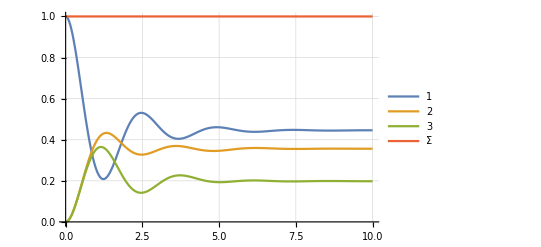

```mathematica
vv = {n1[t], n2[t], n3[t], f1[t], f2[t], f3[t], f4[t]};
IC = {n1[0] == 1, n2[0] == 0, n3[0] == 0, f1[0] == 0, f2[0]== 0, f3[0] == 0,f4[0] == 0};
tMax = 10;
(*Manipulate[*)
δ0 = 1;
ωr0 =1;
{n1S, n2S, n3S, fS,fS,fS,fS}=NDSolveValue[D[vv,t] == (EM /. {δ-> δ0, ωr-> ωr0}).vv && IC,vv, {t,0, tMax}];
n1S=n1S⟦0⟧;n2S=n2S⟦0⟧;n3S=n3S⟦0⟧;
Plot[{n1S[t], n2S[t], n3S[t], n1S[t]+n2S[t]+n3S[t]}, {t, 0, tMax}, GridLines->Automatic, PlotLegends->{1, 2, 3, "Σ"}]
(*, {{δ0, 1}, 0, 10}, {ωr0, 0.1, 2}]*)
```